```mathematica
(* I mangled "methods" 1-4 with r->x and h->y changes that I tried to fix up -- anyways only working correctly without ad hoc removal of pieces is method 5 anyways *)
```

```mathematica
gcovks={{-1+(2 M x)/(x^2+a^2 Cos[y]^2),(2 M x)/(x^2+a^2 Cos[y]^2),0,-(2 a M x Sin[y]^2)/(x^2+a^2 Cos[y]^2)},{(2 M x)/(x^2+a^2 Cos[y]^2),1+(2 M x)/(x^2+a^2 Cos[y]^2),0,-a (1+(2 M x)/(x^2+a^2 Cos[y]^2)) Sin[y]^2},{0,0,x^2+a^2 Cos[y]^2,0},{-(2 a M x Sin[y]^2)/(x^2+a^2 Cos[y]^2),-a (1+(2 M x)/(x^2+a^2 Cos[y]^2)) Sin[y]^2,0,Sin[y]^2 (x^2+a^2 Cos[y]^2+a^2 (1+(2 M x)/(x^2+a^2 Cos[y]^2)) Sin[y]^2)}}
```

{{-1+(2 M x)/(x^2+a^2 Cos[y]^2),(2 M x)/(x^2+a^2 Cos[y]^2),0,-(2 a M x Sin[y]^2)/(x^2+a^2 Cos[y]^2)},{(2 M x)/(x^2+a^2 Cos[y]^2),1+(2 M x)/(x^2+a^2 Cos[y]^2),0,-a (1+(2 M x)/(x^2+a^2 Cos[y]^2)) Sin[y]^2},{0,0,x^2+a^2 Cos[y]^2,0},{-(2 a M x Sin[y]^2)/(x^2+a^2 Cos[y]^2),-a (1+(2 M x)/(x^2+a^2 Cos[y]^2)) Sin[y]^2,0,Sin[y]^2 (x^2+a^2 Cos[y]^2+a^2 (1+(2 M x)/(x^2+a^2 Cos[y]^2)) Sin[y]^2)}}

```mathematica
gcovks[[1,1]]//.{a->0}
```

-1+(2 M)/x

```mathematica
gcovbl={{-1+(2 M x)/(x^2+a^2 Cos[y]^2),0,0,-(2 a M x Sin[y]^2)/(x^2+a^2 Cos[y]^2)},{0,(x^2+a^2 Cos[y]^2)/(a^2-2 M x+x^2),0,0},{0,0,x^2+a^2 Cos[y]^2,0},{-(2 a M x Sin[y]^2)/(x^2+a^2 Cos[y]^2),0,0,(Sin[y]^2 ((a^2+x^2)^2-a^2 (a^2+x (-2 M+x)) Sin[y]^2))/(x^2+a^2 Cos[y]^2)}}
```

{{-1+(2 M x)/(x^2+a^2 Cos[y]^2),0,0,-(2 a M x Sin[y]^2)/(x^2+a^2 Cos[y]^2)},{0,(x^2+a^2 Cos[y]^2)/(a^2-2 M x+x^2),0,0},{0,0,x^2+a^2 Cos[y]^2,0},{-(2 a M x Sin[y]^2)/(x^2+a^2 Cos[y]^2),0,0,(Sin[y]^2 ((a^2+x^2)^2-a^2 (a^2+x (-2 M+x)) Sin[y]^2))/(x^2+a^2 Cos[y]^2)}}

```mathematica
gcovtovbl={{-ⅇ^(2 phivsr[x]),0,0,0},{0,x/(x-2 Mvsr[x]),0,0},{0,0,x^2,0},{0,0,0,x^2 Sin[y]^2}}
```

{{-ⅇ^(2 phivsr[x]),0,0,0},{0,x/(x-2 Mvsr[x]),0,0},{0,0,x^2,0},{0,0,0,x^2 Sin[y]^2}}

```mathematica
gcovtovvsq={{-ⅇ^(2 phivsr[x]),0,0,0},{0,x/(x+vrsq x-2 Mvsr[x]),0,0},{0,0,x^2,0},{0,0,0,x^2 Sin[y]^2}}
```

{{-ⅇ^(2 phivsr[x]),0,0,0},{0,x/(x+vrsq x-2 Mvsr[x]),0,0},{0,0,x^2,0},{0,0,0,x^2 Sin[y]^2}}

```mathematica
gcovpert={{-1-2 phivsr[x],0,0,0},{0,1-2 phivsr[x],0,0},{0,0,x^2,0},{0,0,0,x^2 Sin[y]^2}}
```

{{-1-2 phivsr[x],0,0,0},{0,1-2 phivsr[x],0,0},{0,0,x^2,0},{0,0,0,x^2 Sin[y]^2}}

```mathematica
gcovmink={{-1,0,0,0},{0,1,0,0},{0,0,x^2,0},{0,0,0,x^2 Sin[y]^2}}
```

{{-1,0,0,0},{0,1,0,0},{0,0,x^2,0},{0,0,0,x^2 Sin[y]^2}}

```mathematica
MatrixForm[gcovksa0=gcovks//.{a->0}]
MatrixForm[gcovbla0=gcovbl//.{a->0}]
MatrixForm[gcovtovbl]
MatrixForm[gcovtovvsq]
MatrixForm[gcovpert]
```

(-1+(2 M)/x | (2 M)/x | 0 | 0
(2 M)/x | 1+(2 M)/x | 0 | 0
0 | 0 | x^2 | 0
0 | 0 | 0 | x^2 Sin[y]^2)

(-1+(2 M)/x | 0 | 0 | 0
0 | x^2/(-2 M x+x^2) | 0 | 0
0 | 0 | x^2 | 0
0 | 0 | 0 | x^2 Sin[y]^2)

(-ⅇ^(2 phivsr[x]) | 0 | 0 | 0
0 | x/(x-2 Mvsr[x]) | 0 | 0
0 | 0 | x^2 | 0
0 | 0 | 0 | x^2 Sin[y]^2)

(-ⅇ^(2 phivsr[x]) | 0 | 0 | 0
0 | x/(x+vrsq x-2 Mvsr[x]) | 0 | 0
0 | 0 | x^2 | 0
0 | 0 | 0 | x^2 Sin[y]^2)

(-1-2 phivsr[x] | 0 | 0 | 0
0 | 1-2 phivsr[x] | 0 | 0
0 | 0 | x^2 | 0
0 | 0 | 0 | x^2 Sin[y]^2)

```mathematica
(* Construct general metric in standard foliation form *)
```

```mathematica
Clear[alpha]
dx={dt,dr,dh,dp}
beta={0,b2,b3,b4}
gammaij={{0,0,0,0},{0,gcov22,gcov23,gcov24},{0,gcov23,gcov33,gcov34},{0,gcov24,gcov34,gcov44}}
MatrixForm[gammaij]
ds2=-alphasq*dt^2+Sum[gammaij[[i,j]]*(dx[[i]]+beta[[i]]*dt)*(dx[[j]]+beta[[j]]*dt),{i,2,4},{j,2,4}]
Clear[ds22]
ds22[y_]:=Coefficient[ds2,y];
gcov0={{ds22[dt*dt],ds22[dt*dr]/2,ds22[dt*dh]/2,ds22[dt*dp]/2},{ds22[dr*dt]/2,ds22[dr*dr],ds22[dr*dh]/2,ds22[dr*dp]/2},{ds22[dh*dt]/2,ds22[dh*dr]/2,ds22[dh*dh],ds22[dh*dp]/2},{ds22[dp*dt]/2,ds22[dp*dr]/2,ds22[dp*dh]/2,ds22[dp*dp]}};
MatrixForm[gcov0]
```

{dt,dr,dh,dp}

{0,b2,b3,b4}

{{0,0,0,0},{0,gcov22,gcov23,gcov24},{0,gcov23,gcov33,gcov34},{0,gcov24,gcov34,gcov44}}

(0 | 0 | 0 | 0
0 | gcov22 | gcov23 | gcov24
0 | gcov23 | gcov33 | gcov34
0 | gcov24 | gcov34 | gcov44)

-alphasq dt^2+(dr+b2 dt)^2 gcov22+2 (dr+b2 dt) (dh+b3 dt) gcov23+2 (dr+b2 dt) (dp+b4 dt) gcov24+(dh+b3 dt)^2 gcov33+2 (dh+b3 dt) (dp+b4 dt) gcov34+(dp+b4 dt)^2 gcov44

(-alphasq+b2^2 gcov22+2 b2 b3 gcov23+2 b2 b4 gcov24+b3^2 gcov33+2 b3 b4 gcov34+b4^2 gcov44 | 1/2 (2 b2 gcov22+2 b3 gcov23+2 b4 gcov24) | 1/2 (2 b2 gcov23+2 b3 gcov33+2 b4 gcov34) | 1/2 (2 b2 gcov24+2 b3 gcov34+2 b4 gcov44)
1/2 (2 b2 gcov22+2 b3 gcov23+2 b4 gcov24) | gcov22 | gcov23 | gcov24
1/2 (2 b2 gcov23+2 b3 gcov33+2 b4 gcov34) | gcov23 | gcov33 | gcov34
1/2 (2 b2 gcov24+2 b3 gcov34+2 b4 gcov44) | gcov24 | gcov34 | gcov44)

```mathematica
(* Setup metric with known entries *)
```

```mathematica
ds2gen=gcov11*dt^2+gcov22*dr^2+gcov33*dh^2+gcov44*dp^2+2*(gcov12*dt*dr+gcov13*dt*dh+gcov14*dt*dp+gcov23*dr*dh+gcov24*dr*dp+gcov34*dh*dp);
Clear[ds22gen]
ds22[y_]:=Coefficient[ds2gen,y];
gcovgen={{ds22[dt*dt],ds22[dt*dr]/2,ds22[dt*dh]/2,ds22[dt*dp]/2},{ds22[dr*dt]/2,ds22[dr*dr],ds22[dr*dh]/2,ds22[dr*dp]/2},{ds22[dh*dt]/2,ds22[dh*dr]/2,ds22[dh*dh],ds22[dh*dp]/2},{ds22[dp*dt]/2,ds22[dp*dr]/2,ds22[dp*dh]/2,ds22[dp*dp]}};
MatrixForm[gcovgen]
```

(gcov11 | gcov12 | gcov13 | gcov14
gcov12 | gcov22 | gcov23 | gcov24
gcov13 | gcov23 | gcov33 | gcov34
gcov14 | gcov24 | gcov34 | gcov44)

```mathematica
(* Solve for known entries in terms of standard foliation *)
```

```mathematica
eqns=Table[gcov0[[1+Mod[i-1,4],1+IntegerPart[(i-1)/4]]]==gcovgen[[1+Mod[i-1,4],1+IntegerPart[(i-1)/4]]],{i,1,4}];
Solve[eqns,{gcov11,gcov12,gcov13,gcov14}];
solalpha=FullSimplify[Solve[eqns,{alphasq,b2,b3,b4}]]
```

{{alphasq→(gcov14^2 (gcov23^2-gcov22 gcov33)+2 gcov14 (-gcov13 gcov23 gcov24+gcov12 gcov24 gcov33+gcov13 gcov22 gcov34-gcov12 gcov23 gcov34)+gcov13^2 (gcov24^2-gcov22 gcov44)+2 gcov12 gcov13 (-gcov24 gcov34+gcov23 gcov44)+gcov12^2 (gcov34^2-gcov33 gcov44)-gcov11 (gcov24^2 gcov33-2 gcov23 gcov24 gcov34+gcov23^2 gcov44+gcov22 (gcov34^2-gcov33 gcov44)))/(gcov24^2 gcov33-2 gcov23 gcov24 gcov34+gcov23^2 gcov44+gcov22 (gcov34^2-gcov33 gcov44)),b2→(gcov14 gcov24 gcov33-gcov14 gcov23 gcov34-gcov13 gcov24 gcov34+gcov12 gcov34^2+gcov13 gcov23 gcov44-gcov12 gcov33 gcov44)/(gcov24^2 gcov33-2 gcov23 gcov24 gcov34+gcov22 gcov34^2+gcov23^2 gcov44-gcov22 gcov33 gcov44),b3→(-gcov14 gcov23 gcov24+gcov13 gcov24^2+gcov14 gcov22 gcov34-gcov12 gcov24 gcov34-gcov13 gcov22 gcov44+gcov12 gcov23 gcov44)/(gcov24^2 gcov33-2 gcov23 gcov24 gcov34+gcov23^2 gcov44+gcov22 (gcov34^2-gcov33 gcov44)),b4→(gcov14 gcov23^2-gcov13 gcov23 gcov24-gcov14 gcov22 gcov33+gcov12 gcov24 gcov33+gcov13 gcov22 gcov34-gcov12 gcov23 gcov34)/(gcov24^2 gcov33-2 gcov23 gcov24 gcov34+gcov22 gcov34^2+gcov23^2 gcov44-gcov22 gcov33 gcov44)}}

```mathematica
(* Check that foliation is consistent with expectations *)
```

```mathematica
gcongen=Inverse[gcovgen];
gcongen[[1,1]]
(* check that alpha=1/sqrt{-g^tt} -> alphasq = -1/g^tt *)
myalphasq=alphasq/.solalpha
FullSimplify[myalphasq+1/gcongen[[1,1]]]
```

(-gcov24^2 gcov33+2 gcov23 gcov24 gcov34-gcov22 gcov34^2-gcov23^2 gcov44+gcov22 gcov33 gcov44)/(gcov14^2 gcov23^2-2 gcov13 gcov14 gcov23 gcov24+gcov13^2 gcov24^2-gcov14^2 gcov22 gcov33+2 gcov12 gcov14 gcov24 gcov33-gcov11 gcov24^2 gcov33+2 gcov13 gcov14 gcov22 gcov34-2 gcov12 gcov14 gcov23 gcov34-2 gcov12 gcov13 gcov24 gcov34+2 gcov11 gcov23 gcov24 gcov34+gcov12^2 gcov34^2-gcov11 gcov22 gcov34^2-gcov13^2 gcov22 gcov44+2 gcov12 gcov13 gcov23 gcov44-gcov11 gcov23^2 gcov44-gcov12^2 gcov33 gcov44+gcov11 gcov22 gcov33 gcov44)

{(gcov14^2 (gcov23^2-gcov22 gcov33)+2 gcov14 (-gcov13 gcov23 gcov24+gcov12 gcov24 gcov33+gcov13 gcov22 gcov34-gcov12 gcov23 gcov34)+gcov13^2 (gcov24^2-gcov22 gcov44)+2 gcov12 gcov13 (-gcov24 gcov34+gcov23 gcov44)+gcov12^2 (gcov34^2-gcov33 gcov44)-gcov11 (gcov24^2 gcov33-2 gcov23 gcov24 gcov34+gcov23^2 gcov44+gcov22 (gcov34^2-gcov33 gcov44)))/(gcov24^2 gcov33-2 gcov23 gcov24 gcov34+gcov23^2 gcov44+gcov22 (gcov34^2-gcov33 gcov44))}

{0}

```mathematica
(* Check beta *)
```

```mathematica
(*etagen={-alpha,0,0,0}*)
(*betagen=Table[alpha^2*gcongen2[[1,j]],{j,2,4}]*)
(* check beta *)
myalphasq=alphasq/.solalpha[[1]];
mybeta=beta/.solalpha[[1]];
FullSimplify[Table[myalphasq*gcongen[[1,j]]-mybeta[[j]],{j,2,4}]]
(* So consistent with expectations *)
```

{0,0,0}

```mathematica
(* Transform bl->ks to see if transformation properly setup *)
```

```mathematica
delta=r^2-2*M*r+a^2;
sigma=r^2+a^2*Cos[h]^2;
A=(r^2+a^2)^2-delta*a^2*Sin[h]^2;
rp=M+Sqrt[M^2-a^2];
```

```mathematica
bl2ks={{1,2*M*x/delta,0,0},{0,1,0,0},{0,0,1,0},{0,a/delta,0,1}}//.{r->x,h->y};
MatrixForm[bl2ks]
ks2bl=Inverse[bl2ks];
```

(1 | (2 M x)/(a^2-2 M x+x^2) | 0 | 0
0 | 1 | 0 | 0
0 | 0 | 1 | 0
0 | a/(a^2-2 M x+x^2) | 0 | 1)

```mathematica
testgcovks=FullSimplify[Table[Sum[gcovbl[[i,j]]*(Inverse[bl2ks][[i,ii]]*Inverse[bl2ks][[j,jj]])//.{r->x,h->y},{i,1,4},{j,1,4}],{ii,1,4},{jj,1,4}]]
```

{{-1+(2 M x)/(x^2+a^2 Cos[y]^2),(2 M x)/(x^2+a^2 Cos[y]^2),0,-(2 a M x Sin[y]^2)/(x^2+a^2 Cos[y]^2)},{(2 M x)/(x^2+a^2 Cos[y]^2),1+(4 M x)/(a^2+2 x^2+a^2 Cos[2 y]),0,-(a (a^2+2 x (2 M+x)+a^2 Cos[2 y]) Sin[y]^2)/(a^2+2 x^2+a^2 Cos[2 y])},{0,0,x^2+a^2 Cos[y]^2,0},{-(2 a M x Sin[y]^2)/(x^2+a^2 Cos[y]^2),-(a (a^2+2 x (2 M+x)+a^2 Cos[2 y]) Sin[y]^2)/(a^2+2 x^2+a^2 Cos[2 y]),0,(Sin[y]^2 ((a^2+x^2)^2-a^2 (a^2+x (-2 M+x)) Sin[y]^2))/(x^2+a^2 Cos[y]^2)}}

```mathematica
FullSimplify[testgcovks-gcovks]
```

{{0,0,0,0},{0,0,0,0},{0,0,0,0},{0,0,0,0}}

```mathematica
(* So transformation is correct *)
```

```mathematica
(* Consider transformation for TOV *)
```

```mathematica
bl2ks={{1,2*Mvsr[r]*r/(r^2-2*Mvsr[r]*r),0,0},{0,1,0,0},{0,0,1,0},{0,a/delta,0,1}}//.{a->0,r->x,h->y}
```

{{1,(2 x Mvsr[x])/(x^2-2 x Mvsr[x]),0,0},{0,1,0,0},{0,0,1,0},{0,0,0,1}}

```mathematica
bl2ks={{1,2*phivsr[r]*x^2/delta,0,0},{0,1,0,0},{0,0,1,0},{0,a/delta,0,1}}//.{a->0,r->x,h->y}
```

{{1,(2 x^2 phivsr[x])/(-2 M x+x^2),0,0},{0,1,0,0},{0,0,1,0},{0,0,0,1}}

```mathematica
(* Setup transformation for TOV -> KS TOV as in that paper *)
```

```mathematica
mygcov=gcovtovvsq
AAA=Sqrt[-mygcov[[1,1]]]
BBB=Sqrt[mygcov[[2,2]]]
```

{{-ⅇ^(2 phivsr[x]),0,0,0},{0,x/(x+vrsq x-2 Mvsr[x]),0,0},{0,0,x^2,0},{0,0,0,x^2 Sin[y]^2}}

√(ⅇ^(2 phivsr[x]))

√(x/(x+vrsq x-2 Mvsr[x]))

```mathematica
(* old version in that paper *)
```

```mathematica
tov2tovks={{1,0,0,0},{0,BBB/AAA-1,0,0},{0,0,1,0},{0,0,0,1}} (* odd *)
tov2tovks=FullSimplify[{{1,BBB/AAA-1,0,0},{0,1,0,0},{0,0,1,0},{0,0,0,1}},{Im[x]==0,Im[a]==0,Im[y]==0,Im[M]==0}]
MatrixForm[tov2tovks]
(* test *)
testgcovtovks=
FullSimplify[Table[Sum[mygcov[[i,j]]*(Inverse[tov2tovks][[i,ii]]*Inverse[tov2tovks][[j,jj]]),{i,1,4},{j,1,4}],{ii,1,4},{jj,1,4}]];
MatrixForm[testgcovtovks]
```

{{1,0,0,0},{0,-1+(√(x/(x+vrsq x-2 Mvsr[x])))/(√(ⅇ^(2 phivsr[x]))),0,0},{0,0,1,0},{0,0,0,1}}

{{1,-1+(√(x/(x+vrsq x-2 Mvsr[x])))/(√(ⅇ^(2 phivsr[x]))),0,0},{0,1,0,0},{0,0,1,0},{0,0,0,1}}

(1 | -1+(√(x/(x+vrsq x-2 Mvsr[x])))/(√(ⅇ^(2 phivsr[x]))) | 0 | 0
0 | 1 | 0 | 0
0 | 0 | 1 | 0
0 | 0 | 0 | 1)

(-ⅇ^(2 phivsr[x]) | -ⅇ^(2 phivsr[x])+√(ⅇ^(2 phivsr[x])) √(x/(x+vrsq x-2 Mvsr[x])) | 0 | 0
-ⅇ^(2 phivsr[x])+√(ⅇ^(2 phivsr[x])) √(x/(x+vrsq x-2 Mvsr[x])) | -ⅇ^(2 phivsr[x])+2 √(ⅇ^(2 phivsr[x])) √(x/(x+vrsq x-2 Mvsr[x])) | 0 | 0
0 | 0 | x^2 | 0
0 | 0 | 0 | x^2 Sin[y]^2)

```mathematica
(* new version in paper *)
```

```mathematica
tov2tovks={{1,0,0,0},{0,BBB/AAA-1/(AAA*BBB),0,0},{0,0,1,0},{0,0,0,1}} (* wow, but odd *)
tov2tovks={{1,0,0,0},{BBB/AAA-1/(AAA*BBB),1,0,0},{0,0,1,0},{0,0,0,1}} (* uh, bad *)
tov2tovks={{1,BBB/AAA-1/(AAA*BBB),0,0},{0,1,0,0},{0,0,1,0},{0,0,0,1}}
MatrixForm[tov2tovks]
```

{{1,0,0,0},{0,-1/(√(ⅇ^(2 phivsr[x])) √(x/(x+vrsq x-2 Mvsr[x])))+(√(x/(x+vrsq x-2 Mvsr[x])))/(√(ⅇ^(2 phivsr[x]))),0,0},{0,0,1,0},{0,0,0,1}}

{{1,0,0,0},{-1/(√(ⅇ^(2 phivsr[x])) √(x/(x+vrsq x-2 Mvsr[x])))+(√(x/(x+vrsq x-2 Mvsr[x])))/(√(ⅇ^(2 phivsr[x]))),1,0,0},{0,0,1,0},{0,0,0,1}}

{{1,-1/(√(ⅇ^(2 phivsr[x])) √(x/(x+vrsq x-2 Mvsr[x])))+(√(x/(x+vrsq x-2 Mvsr[x])))/(√(ⅇ^(2 phivsr[x]))),0,0},{0,1,0,0},{0,0,1,0},{0,0,0,1}}

(1 | -1/(√(ⅇ^(2 phivsr[x])) √(x/(x+vrsq x-2 Mvsr[x])))+(√(x/(x+vrsq x-2 Mvsr[x])))/(√(ⅇ^(2 phivsr[x]))) | 0 | 0
0 | 1 | 0 | 0
0 | 0 | 1 | 0
0 | 0 | 0 | 1)

```mathematica
(* Form KS version of TOV metric *)
```

```mathematica
mygcovtovks=FullSimplify[Table[Sum[mygcov[[i,j]]*(Inverse[tov2tovks][[i,ii]]*Inverse[tov2tovks][[j,jj]]),{i,1,4},{j,1,4}],{ii,1,4},{jj,1,4}]]
```

{{-ⅇ^(2 phivsr[x]),(√(ⅇ^(2 phivsr[x])) √(x/(x+vrsq x-2 Mvsr[x])) (-vrsq x+2 Mvsr[x]))/x,0,0},{(√(ⅇ^(2 phivsr[x])) √(x/(x+vrsq x-2 Mvsr[x])) (-vrsq x+2 Mvsr[x]))/x,1-vrsq+(2 Mvsr[x])/x,0,0},{0,0,x^2,0},{0,0,0,x^2 Sin[y]^2}}

```mathematica
MatrixForm[mygcovtovks=FullSimplify[mygcovtovks,{Im[x]==0,Im[y]==0,Im[a]==0}]]
```

(-ⅇ^(2 phivsr[x]) | (√(ⅇ^(2 phivsr[x])) √(x/(x+vrsq x-2 Mvsr[x])) (-vrsq x+2 Mvsr[x]))/x | 0 | 0
(√(ⅇ^(2 phivsr[x])) √(x/(x+vrsq x-2 Mvsr[x])) (-vrsq x+2 Mvsr[x]))/x | 1-vrsq+(2 Mvsr[x])/x | 0 | 0
0 | 0 | x^2 | 0
0 | 0 | 0 | x^2 Sin[y]^2)

```mathematica
(* See behavior for small phi *)
```

```mathematica
MatrixForm[Normal[Series[mygcovtovks,{phivsr[x],0,1}]]]
```

(-1-2 phivsr[x] | (√(x/(x+vrsq x-2 Mvsr[x])) (-vrsq x+2 Mvsr[x]))/x+(√(x/(x+vrsq x-2 Mvsr[x])) (-vrsq x+2 Mvsr[x]) phivsr[x])/x | 0 | 0
(√(x/(x+vrsq x-2 Mvsr[x])) (-vrsq x+2 Mvsr[x]))/x+(√(x/(x+vrsq x-2 Mvsr[x])) (-vrsq x+2 Mvsr[x]) phivsr[x])/x | 1-vrsq+(2 Mvsr[x])/x | 0 | 0
0 | 0 | x^2 | 0
0 | 0 | 0 | x^2 Sin[y]^2)

```mathematica
(* Compare with KS black hole for a=0 *)
```

```mathematica
MatrixForm[gcovksa0]
```

(-1+(2 M)/x | (2 M)/x | 0 | 0
(2 M)/x | 1+(2 M)/x | 0 | 0
0 | 0 | x^2 | 0
0 | 0 | 0 | x^2 Sin[y]^2)

```mathematica
(* PLEASE SKIP METHODS 1-4 and SKIP TO METHOD 5 *)
```

```mathematica
(* HERE BEGINS VERSION 1 OF TRYING TO FORM MIXED METRIC *)
```

```mathematica
mixedkstov=({{-Exp[2*phivsr[r]+Log[1-(2 M)/x]], (2 M)/x+(2 √(ⅇ^(2 phivsr[r])) √(r/(r-2 Mvsr[r])) Mvsr[r])/r, 0, 0}, {(2 M)/x+(2 √(ⅇ^(2 phivsr[r])) √(r/(r-2 Mvsr[r])) Mvsr[r])/r, 1+(2 M)/x+2Mvsr[r]/r, 0, 0}, {0, 0, x^2, 0}, {0, 0, 0, x^2 Sin[y]^2}})//.{r->x,h->y}
MatrixForm[mixedkstov//.{phivsr[x]->0,Mvsr[x]->0}]
MatrixForm[mixedkstov//.{M->0}]
MatrixForm[FullSimplify[mixedkstov//.{phivsr[x]->Log[1-2*M/x]/2,Mvsr[x]->M},{x>2*M,M>0}]]
```

{{-ⅇ^(2 phivsr[x]) (1-(2 M)/x),(2 M)/x+(2 √(ⅇ^(2 phivsr[x])) √(x/(x-2 Mvsr[x])) Mvsr[x])/x,0,0},{(2 M)/x+(2 √(ⅇ^(2 phivsr[x])) √(x/(x-2 Mvsr[x])) Mvsr[x])/x,1+(2 M)/x+(2 Mvsr[x])/x,0,0},{0,0,x^2,0},{0,0,0,x^2 Sin[y]^2}}

(-1+(2 M)/x | (2 M)/x | 0 | 0
(2 M)/x | 1+(2 M)/x | 0 | 0
0 | 0 | x^2 | 0
0 | 0 | 0 | x^2 Sin[y]^2)

(-ⅇ^(2 phivsr[x]) | (2 √(ⅇ^(2 phivsr[x])) √(x/(x-2 Mvsr[x])) Mvsr[x])/x | 0 | 0
(2 √(ⅇ^(2 phivsr[x])) √(x/(x-2 Mvsr[x])) Mvsr[x])/x | 1+(2 Mvsr[x])/x | 0 | 0
0 | 0 | x^2 | 0
0 | 0 | 0 | x^2 Sin[y]^2)

(-(-2 M+x)^2/x^2 | (4 M)/x | 0 | 0
(4 M)/x | 1+(4 M)/x | 0 | 0
0 | 0 | x^2 | 0
0 | 0 | 0 | x^2 Sin[y]^2)

```mathematica
MatrixForm[gcovks//.{a->0,M->(2*Mp)}]
```

(-1+(4 Mp)/x | (4 Mp)/x | 0 | 0
(4 Mp)/x | 1+(4 Mp)/x | 0 | 0
0 | 0 | x^2 | 0
0 | 0 | 0 | x^2 Sin[y]^2)

```mathematica
Solve[-Exp[2*phivsr[x]+Log[1-(2 M)/x]]==-Exp[Log[1-(4 M)/x]],phivsr[x]]
```

Solve::ifun: Inverse functions are being used by Solve, so some solutions may not be found; use Reduce for complete solution information.

{{phivsr[x]→Log[-(√(4 M-x))/(√(2 M-x))]},{phivsr[x]→Log[(√(4 M-x))/(√(2 M-x))]}}

```mathematica
(* What does the above mean?  Potentials are highly non-linear for BH *)
```

```mathematica
-AAA^2
FullSimplify[2*AAA*BBB*(1-BBB^(-2))]
FullSimplify[(2-BBB^(-2))]
```

-ⅇ^(2 phivsr[x])

-(2 √(ⅇ^(2 phivsr[x])) (vrsq x-2 Mvsr[x]) √(x/(x+vrsq x-2 Mvsr[x])))/x

1-vrsq+(2 Mvsr[x])/x

```mathematica
(* so same as http://arxiv.org/PS_cache/gr-qc/pdf/0605/0605018v1.pdf *)
```

```mathematica
(* HERE BEGINS VERSION 2 OF TRYING TO FORM MIXED METRIC *)
```

```mathematica
MatrixForm[gcovks]
```

(-1+(2 M x)/(x^2+a^2 Cos[y]^2) | (2 M x)/(x^2+a^2 Cos[y]^2) | 0 | -(2 a M x Sin[y]^2)/(x^2+a^2 Cos[y]^2)
(2 M x)/(x^2+a^2 Cos[y]^2) | 1+(2 M x)/(x^2+a^2 Cos[y]^2) | 0 | -a (1+(2 M x)/(x^2+a^2 Cos[y]^2)) Sin[y]^2
0 | 0 | x^2+a^2 Cos[y]^2 | 0
-(2 a M x Sin[y]^2)/(x^2+a^2 Cos[y]^2) | -a (1+(2 M x)/(x^2+a^2 Cos[y]^2)) Sin[y]^2 | 0 | Sin[y]^2 (x^2+a^2 Cos[y]^2+a^2 (1+(2 M x)/(x^2+a^2 Cos[y]^2)) Sin[y]^2))

```mathematica
MatrixForm[FullSimplify[mygcovtovks//.{phivsr[x]->Log[1-2*M*x/(x^2+a^2*Cos[y]^2)]/2,Mvsr[x]->(2 M x^2)/(a^2+2 x^2+a^2 Cos[2 y])},{x>2*M,M>0,y>0}]]
```

(-1+(2 M x)/(x^2+a^2 Cos[y]^2) | √(1-(2 M x)/(x^2+a^2 Cos[y]^2)) √(1/(1+vrsq-(4 M x)/(a^2+2 x^2+a^2 Cos[2 y]))) (-vrsq+(4 M x)/(a^2+2 x^2+a^2 Cos[2 y])) | 0 | 0
√(1-(2 M x)/(x^2+a^2 Cos[y]^2)) √(1/(1+vrsq-(4 M x)/(a^2+2 x^2+a^2 Cos[2 y]))) (-vrsq+(4 M x)/(a^2+2 x^2+a^2 Cos[2 y])) | 1-vrsq+(4 M x)/(a^2+2 x^2+a^2 Cos[2 y]) | 0 | 0
0 | 0 | x^2 | 0
0 | 0 | 0 | x^2 Sin[y]^2)

```mathematica
Solve[2*myM/r==(4 M r)/(a^2+2 r^2+a^2 Cos[2 h]),myM]//.{r->x,h->y}
```

{{myM→(2 M x^2)/(a^2+2 x^2+a^2 Cos[2 y])}}

```mathematica
FullSimplify[(4 M r √(1-(2 M r)/(r^2+a^2 Cos[h]^2)) √(1+(4 M r)/(a^2+2 r (-2 M+r)+a^2 Cos[2 h])))/(a^2+2 r^2+a^2 Cos[2 h])-(2 M r)/(r^2+a^2 Cos[h]^2),{r>2*M}]//.{r->10,M->1,a->.7,h->Pi/4}
```

0.

```mathematica
finalmixed=({{-ⅇ^(2 phivsr[r]), (2  √(ⅇ^(2 phivsr[r])/(1-2 Mvsr[r]/r)) Mvsr[r])/r, 0, -(2 a M r Sin[h]^2)/(r^2+a^2 Cos[h]^2)}, {(2  √(ⅇ^(2 phivsr[r])/(1-2 Mvsr[r]/r)) Mvsr[r])/r, 1+2Mvsr[r]/r, 0, -(a (a^2+2 r (2 M+r)+a^2 Cos[2 h]) Sin[h]^2)/(a^2+2 r^2+a^2 Cos[2 h])}, {0, 0, r^2+a^2 Cos[h]^2, 0}, {-(2 a M r Sin[h]^2)/(r^2+a^2 Cos[h]^2), -(a (a^2+2 r (2 M+r)+a^2 Cos[2 h]) Sin[h]^2)/(a^2+2 r^2+a^2 Cos[2 h]), 0, (Sin[h]^2 ((a^2+r^2)^2-a^2 (a^2+r (-2 M+r)) Sin[h]^2))/(r^2+a^2 Cos[h]^2)}})//.{r->x,h->y}
```

{{-ⅇ^(2 phivsr[x]),(2 Mvsr[x] √(ⅇ^(2 phivsr[x])/(1-(2 Mvsr[x])/x)))/x,0,-(2 a M x Sin[y]^2)/(x^2+a^2 Cos[y]^2)},{(2 Mvsr[x] √(ⅇ^(2 phivsr[x])/(1-(2 Mvsr[x])/x)))/x,1+(2 Mvsr[x])/x,0,-(a (a^2+2 x (2 M+x)+a^2 Cos[2 y]) Sin[y]^2)/(a^2+2 x^2+a^2 Cos[2 y])},{0,0,x^2+a^2 Cos[y]^2,0},{-(2 a M x Sin[y]^2)/(x^2+a^2 Cos[y]^2),-(a (a^2+2 x (2 M+x)+a^2 Cos[2 y]) Sin[y]^2)/(a^2+2 x^2+a^2 Cos[2 y]),0,(Sin[y]^2 ((a^2+x^2)^2-a^2 (a^2+x (-2 M+x)) Sin[y]^2))/(x^2+a^2 Cos[y]^2)}}

```mathematica
MatrixForm[finalmixed]
```

(-ⅇ^(2 phivsr[x]) | (2 Mvsr[x] √(ⅇ^(2 phivsr[x])/(1-(2 Mvsr[x])/x)))/x | 0 | -(2 a M x Sin[y]^2)/(x^2+a^2 Cos[y]^2)
(2 Mvsr[x] √(ⅇ^(2 phivsr[x])/(1-(2 Mvsr[x])/x)))/x | 1+(2 Mvsr[x])/x | 0 | -(a (a^2+2 x (2 M+x)+a^2 Cos[2 y]) Sin[y]^2)/(a^2+2 x^2+a^2 Cos[2 y])
0 | 0 | x^2+a^2 Cos[y]^2 | 0
-(2 a M x Sin[y]^2)/(x^2+a^2 Cos[y]^2) | -(a (a^2+2 x (2 M+x)+a^2 Cos[2 y]) Sin[y]^2)/(a^2+2 x^2+a^2 Cos[2 y]) | 0 | (Sin[y]^2 ((a^2+x^2)^2-a^2 (a^2+x (-2 M+x)) Sin[y]^2))/(x^2+a^2 Cos[y]^2))

```mathematica
finalmixedks=finalmixed//.{Q[r]->1-2*M*r/(r^2+a^2*Cos[h]^2),Mvsr[r]->(2 M r^2)/(a^2+2 r^2+a^2 Cos[2 h])}//.{r->x,h->y}
```

{{-ⅇ^(2 phivsr[x]),(2 Mvsr[x] √(ⅇ^(2 phivsr[x])/(1-(2 Mvsr[x])/x)))/x,0,-(2 a M x Sin[y]^2)/(x^2+a^2 Cos[y]^2)},{(2 Mvsr[x] √(ⅇ^(2 phivsr[x])/(1-(2 Mvsr[x])/x)))/x,1+(2 Mvsr[x])/x,0,-(a (a^2+2 x (2 M+x)+a^2 Cos[2 y]) Sin[y]^2)/(a^2+2 x^2+a^2 Cos[2 y])},{0,0,x^2+a^2 Cos[y]^2,0},{-(2 a M x Sin[y]^2)/(x^2+a^2 Cos[y]^2),-(a (a^2+2 x (2 M+x)+a^2 Cos[2 y]) Sin[y]^2)/(a^2+2 x^2+a^2 Cos[2 y]),0,(Sin[y]^2 ((a^2+x^2)^2-a^2 (a^2+x (-2 M+x)) Sin[y]^2))/(x^2+a^2 Cos[y]^2)}}

```mathematica
(* below for CODE *)
```

```mathematica
(* resolved 0/0 in sqrtpiece *)
```

```mathematica
sqrtpiece=√(ⅇ^(2 phistar[r])/(1-(2 Mstar[r]/(1-(2 M r)/(r^2+a^2 Cos[h]^2)))/r))//.{r->x,h->y}
```

√(ⅇ^(2 phistar[x])/(1-(2 Mstar[x])/(x (1-(2 M x)/(x^2+a^2 Cos[y]^2)))))

```mathematica
Solve[1-((2 M r^2)/(a^2+2 r^2+a^2 Cos[2 h]))/r==0,r]//.{h->Pi/2,M->1}//.{r->x,h->y}
```

{{x→0},{x→1}}

```mathematica
fun=((ⅇ^(2 phistar[r]) (1-(2 M r)/(r^2+a^2 Cos[h]^2)))/(1-(4 M r)/(a^2+2 r^2+a^2 Cos[2 h])-(2 Mstar[r])/r))//.{r->x,h->y}
myphimix=Solve[fun==1,phistar[x]][[1,1,2]]//.{r->x,h->y}
```

(ⅇ^(2 phistar[x]) (1-(2 M x)/(x^2+a^2 Cos[y]^2)))/(1-(4 M x)/(a^2+2 x^2+a^2 Cos[2 y])-(2 Mstar[x])/x)

Solve::ifun: Inverse functions are being used by Solve, so some solutions may not be found; use Reduce for complete solution information.

-1/2 Log[1/(1-(4 M x)/(a^2+2 x^2+a^2 Cos[2 y])-(2 Mstar[x])/x)-(2 M x)/((x^2+a^2 Cos[y]^2) (1-(4 M x)/(a^2+2 x^2+a^2 Cos[2 y])-(2 Mstar[x])/x))]

```mathematica
myphimix//.{M->0}
```

-1/2 Log[1/(1-(2 Mstar[x])/x)]

```mathematica
finalmixedks=FullSimplify[finalmixed//.{phivsr[r]->phistar[r]+Log[1-2*M*r/(r^2+a^2*Cos[h]^2)]/2,Mvsr[r]->Mstar[r]+(2 M r^2)/(a^2+2 r^2+a^2 Cos[2 h])}]//.{r->x,h->y}
```

{{-ⅇ^(2 phivsr[x]),(2 √((ⅇ^(2 phivsr[x]) x)/(x-2 Mvsr[x])) Mvsr[x])/x,0,-(2 a M x Sin[y]^2)/(x^2+a^2 Cos[y]^2)},{(2 √((ⅇ^(2 phivsr[x]) x)/(x-2 Mvsr[x])) Mvsr[x])/x,1+(2 Mvsr[x])/x,0,-(a (a^2+2 x (2 M+x)+a^2 Cos[2 y]) Sin[y]^2)/(a^2+2 x^2+a^2 Cos[2 y])},{0,0,x^2+a^2 Cos[y]^2,0},{-(2 a M x Sin[y]^2)/(x^2+a^2 Cos[y]^2),-(a (a^2+2 x (2 M+x)+a^2 Cos[2 y]) Sin[y]^2)/(a^2+2 x^2+a^2 Cos[2 y]),0,(Sin[y]^2 ((a^2+x^2)^2-a^2 (a^2+x (-2 M+x)) Sin[y]^2))/(x^2+a^2 Cos[y]^2)}}

```mathematica
MatrixForm[{{ⅇ^(2 phistar[r]) (-1+(2 M r)/(r^2+a^2 Cos[h]^2)),(2 ((2 M r^2)/(a^2+2 r^2+a^2 Cos[2 h])+Mstar[r]) √((ⅇ^(2 phistar[r]) (1-(2 M r)/(r^2+a^2 Cos[h]^2)))/(1-(4 M r)/(a^2+2 r^2+a^2 Cos[2 h])-(2 Mstar[r])/r)))/r,0,-(2 a M r Sin[h]^2)/(r^2+a^2 Cos[h]^2)},{(2 ((2 M r^2)/(a^2+2 r^2+a^2 Cos[2 h])+Mstar[r]) √((ⅇ^(2 phistar[r]) (1-(2 M r)/(r^2+a^2 Cos[h]^2)))/(1-(4 M r)/(a^2+2 r^2+a^2 Cos[2 h])-(2 Mstar[r])/r)))/r,1+(4 M r)/(a^2+2 r^2+a^2 Cos[2 h])+(2 Mstar[r])/r,0,-(a (a^2+2 r (2 M+r)+a^2 Cos[2 h]) Sin[h]^2)/(a^2+2 r^2+a^2 Cos[2 h])},{0,0,r^2+a^2 Cos[h]^2,0},{-(2 a M r Sin[h]^2)/(r^2+a^2 Cos[h]^2),-(a (a^2+2 r (2 M+r)+a^2 Cos[2 h]) Sin[h]^2)/(a^2+2 r^2+a^2 Cos[2 h]),0,(Sin[h]^2 ((a^2+r^2)^2-a^2 (a^2+r (-2 M+r)) Sin[h]^2))/(r^2+a^2 Cos[h]^2)}}//.{r->x,h->y}]
```

(ⅇ^(2 phistar[x]) (-1+(2 M x)/(x^2+a^2 Cos[y]^2)) | (2 ((2 M x^2)/(a^2+2 x^2+a^2 Cos[2 y])+Mstar[x]) √((ⅇ^(2 phistar[x]) (1-(2 M x)/(x^2+a^2 Cos[y]^2)))/(1-(4 M x)/(a^2+2 x^2+a^2 Cos[2 y])-(2 Mstar[x])/x)))/x | 0 | -(2 a M x Sin[y]^2)/(x^2+a^2 Cos[y]^2)
(2 ((2 M x^2)/(a^2+2 x^2+a^2 Cos[2 y])+Mstar[x]) √((ⅇ^(2 phistar[x]) (1-(2 M x)/(x^2+a^2 Cos[y]^2)))/(1-(4 M x)/(a^2+2 x^2+a^2 Cos[2 y])-(2 Mstar[x])/x)))/x | 1+(4 M x)/(a^2+2 x^2+a^2 Cos[2 y])+(2 Mstar[x])/x | 0 | -(a (a^2+2 x (2 M+x)+a^2 Cos[2 y]) Sin[y]^2)/(a^2+2 x^2+a^2 Cos[2 y])
0 | 0 | x^2+a^2 Cos[y]^2 | 0
-(2 a M x Sin[y]^2)/(x^2+a^2 Cos[y]^2) | -(a (a^2+2 x (2 M+x)+a^2 Cos[2 y]) Sin[y]^2)/(a^2+2 x^2+a^2 Cos[2 y]) | 0 | (Sin[y]^2 ((a^2+x^2)^2-a^2 (a^2+x (-2 M+x)) Sin[y]^2))/(x^2+a^2 Cos[y]^2))

```mathematica
codeform=({{ⅇ^(2 phistar[r]) (-1+(2 M r)/(r^2+a^2 Cos[h]^2)), (2 ((2 M r^2)/(a^2+2 r^2+a^2 Cos[2 h])+Mstar[r]) sqrtpiece)/r, 0, -(2 a M r Sin[h]^2)/(r^2+a^2 Cos[h]^2)}, {(2 ((2 M r^2)/(a^2+2 r^2+a^2 Cos[2 h])+Mstar[r]) sqrtpiece)/r, 1+(4 M r)/(a^2+2 r^2+a^2 Cos[2 h])+(2 Mstar[r])/r, 0, -(a (a^2+2 r (2 M+r)+a^2 Cos[2 h]) Sin[h]^2)/(a^2+2 r^2+a^2 Cos[2 h])}, {0, 0, r^2+a^2 Cos[h]^2, 0}, {-(2 a M r Sin[h]^2)/(r^2+a^2 Cos[h]^2), -(a (a^2+2 r (2 M+r)+a^2 Cos[2 h]) Sin[h]^2)/(a^2+2 r^2+a^2 Cos[2 h]), 0, (Sin[h]^2 ((a^2+r^2)^2-a^2 (a^2+r (-2 M+r)) Sin[h]^2))/(r^2+a^2 Cos[h]^2)}})//.{r->x,h->y}
```

{{ⅇ^(2 phistar[x]) (-1+(2 M x)/(x^2+a^2 Cos[y]^2)),(2 ((2 M x^2)/(a^2+2 x^2+a^2 Cos[2 y])+Mstar[x]) √(ⅇ^(2 phistar[x])/(1-(2 Mstar[x])/(x (1-(2 M x)/(x^2+a^2 Cos[y]^2))))))/x,0,-(2 a M x Sin[y]^2)/(x^2+a^2 Cos[y]^2)},{(2 ((2 M x^2)/(a^2+2 x^2+a^2 Cos[2 y])+Mstar[x]) √(ⅇ^(2 phistar[x])/(1-(2 Mstar[x])/(x (1-(2 M x)/(x^2+a^2 Cos[y]^2))))))/x,1+(4 M x)/(a^2+2 x^2+a^2 Cos[2 y])+(2 Mstar[x])/x,0,-(a (a^2+2 x (2 M+x)+a^2 Cos[2 y]) Sin[y]^2)/(a^2+2 x^2+a^2 Cos[2 y])},{0,0,x^2+a^2 Cos[y]^2,0},{-(2 a M x Sin[y]^2)/(x^2+a^2 Cos[y]^2),-(a (a^2+2 x (2 M+x)+a^2 Cos[2 y]) Sin[y]^2)/(a^2+2 x^2+a^2 Cos[2 y]),0,(Sin[y]^2 ((a^2+x^2)^2-a^2 (a^2+x (-2 M+x)) Sin[y]^2))/(x^2+a^2 Cos[y]^2)}}

```mathematica
finalmixedks//.{a->0.0,phivsr[x]->0.0,Mvsr[x]->0.0,M->1.0,y->Pi/2,x->2.}
```

{{-1.,0.,0,0.},{0.,1.,0,0.},{0,0,4.,0},{0.,0.,0,4.}}

```mathematica
FullSimplify[(finalmixedks-gcovks)//.{M->1.0,a->.71345,y->0.32355,x->3.56}]
```

{{0.457778-ⅇ^(2 phivsr[3.56]),-0.542222+0.749532 √(ⅇ^(2 phivsr[3.56])/(1.78-1. Mvsr[3.56])) Mvsr[3.56],0,0},{-0.542222+0.749532 √(ⅇ^(2 phivsr[3.56])/(1.78-1. Mvsr[3.56])) Mvsr[3.56],-0.542222+0.561798 Mvsr[3.56],0,0.},{0,0,0,0},{0,0.,0,0.}}

```mathematica
MatrixForm[finalmixedks//.{a->0}//.{r->2.0,M->1}]
```

(-ⅇ^(2 phivsr[x]) | (2 √((ⅇ^(2 phivsr[x]) x)/(x-2 Mvsr[x])) Mvsr[x])/x | 0 | 0
(2 √((ⅇ^(2 phivsr[x]) x)/(x-2 Mvsr[x])) Mvsr[x])/x | 1+(2 Mvsr[x])/x | 0 | 0
0 | 0 | x^2 | 0
0 | 0 | 0 | x^2 Sin[y]^2)

```mathematica
finalmixedfinal=FullSimplify[finalmixed//.{phivsr[r]->phistar[r]+Log[1-2*M*r/(r^2+a^2*Cos[h]^2)]/2,Mvsr[r]->Mstar[r]+(2 M r^2)/(a^2+2 r^2+a^2 Cos[2 h])}]
```

{{-ⅇ^(2 phivsr[x]),(2 √((ⅇ^(2 phivsr[x]) x)/(x-2 Mvsr[x])) Mvsr[x])/x,0,-(2 a M x Sin[y]^2)/(x^2+a^2 Cos[y]^2)},{(2 √((ⅇ^(2 phivsr[x]) x)/(x-2 Mvsr[x])) Mvsr[x])/x,1+(2 Mvsr[x])/x,0,-(a (a^2+2 x (2 M+x)+a^2 Cos[2 y]) Sin[y]^2)/(a^2+2 x^2+a^2 Cos[2 y])},{0,0,x^2+a^2 Cos[y]^2,0},{-(2 a M x Sin[y]^2)/(x^2+a^2 Cos[y]^2),-(a (a^2+2 x (2 M+x)+a^2 Cos[2 y]) Sin[y]^2)/(a^2+2 x^2+a^2 Cos[2 y]),0,(Sin[y]^2 ((a^2+x^2)^2-a^2 (a^2+x (-2 M+x)) Sin[y]^2))/(x^2+a^2 Cos[y]^2)}}

```mathematica
finalmixedfinal//.{a->0,Mstar[r]->0,phistar[r]->0}
```

{{-ⅇ^(2 phivsr[x]),(2 √((ⅇ^(2 phivsr[x]) x)/(x-2 Mvsr[x])) Mvsr[x])/x,0,0},{(2 √((ⅇ^(2 phivsr[x]) x)/(x-2 Mvsr[x])) Mvsr[x])/x,1+(2 Mvsr[x])/x,0,0},{0,0,x^2,0},{0,0,0,x^2 Sin[y]^2}}

```mathematica
((1-(2 M r+S)/(r^2+a^2 Cos[h]^2))/(1-(4 M r+S)/(a^2+2 r^2+a^2 Cos[2 h])-(2 Mstar[r])/r))//.{a->0.,Mstar[r]->0.,h->Pi/2,r->2.,M->1.,S->10^(-10)}
```

2.

```mathematica
god=FullSimplify[((1-(2 M r+S)/(r^2+a^2 Cos[h]^2))/(1-(4 M r+S)/(a^2+2 r^2+a^2 Cos[2 h])-(2 Mstar[r])/r))//.{Mstar[r]->0.,h->Pi/4.,r->M+Sqrt[M^2-a^2],M->1.0}]
```

((1.+√(1.-1. a^2)) (4.-1. a^2+4. √(1.-1. a^2)) (0.-0.5 a^2-1. S))/((-1.-1. √(1.-1. a^2)) (2.-0.5 a^2+2. √(1.-1. a^2)) (a^2+S))

(2.4×10^-9+1. a^4+8.35676×10^-31 √(1.+0. a-1. a^2)+a^2 (8.+1.31072×10^-15 √(1.+0. a-1. a^2)))/(1.59999×10^-9+8. a^2+a^4)

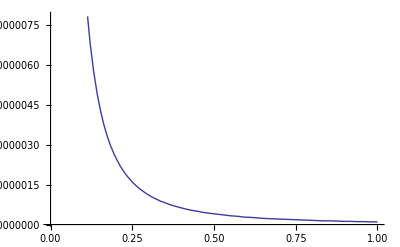

```mathematica
godS=FullSimplify[god//.{S->10^(-10)}]
Plot[godS,{a,0,1}]
```

```mathematica
(* HERE BEGINS VERSION 3 OF TRYING TO FORM MIXED METRIC *)
```

```mathematica
(* the below term might have resolvable 0/0 -- true in a=0 case with Mstar=0 *)
```

```mathematica
badterm=(1-(2 M r)/(r^2+a^2 Cos[h]^2))/(1-(4 M r)/(a^2+2 r^2+a^2 Cos[2 h])-(2 Mstar[r])/r-S)
```

(1-(2 M r)/(r^2+a^2 Cos[h]^2))/(1-S-(4 M r)/(a^2+2 r^2+a^2 Cos[2 h])-(2 Mstar[r])/r)

```mathematica
numbad=(1-(2 M r)/(r^2+a^2 Cos[h]^2))
myrs=Solve[numbad==0,r]
```

1-(2 M r)/(r^2+a^2 Cos[h]^2)

{{r→M-√(M^2-a^2 Cos[h]^2)},{r→M+√(M^2-a^2 Cos[h]^2)}}

```mathematica
denbad=1-(4 M r)/(a^2+2 r^2+a^2 Cos[2 h])+S
Solve[denbad==0,r]
```

1+S-(4 M r)/(a^2+2 r^2+a^2 Cos[2 h])

{{r→(4 M-√(16 M^2-4 (2+2 S) (a^2+a^2 S+a^2 Cos[2 h]+a^2 S Cos[2 h])))/(2 (2+2 S))},{r→(4 M+√(16 M^2-4 (2+2 S) (a^2+a^2 S+a^2 Cos[2 h]+a^2 S Cos[2 h])))/(2 (2+2 S))}}

```mathematica
FullSimplify[(4 M+√(16 M^2-4 (2+2 S) (a^2+a^2 S+a^2 Cos[2 h]+a^2 S Cos[2 h])))/(2 (2+2 S))-(M+√(M^2-a^2 Cos[h]^2))]
```

-√(M^2-a^2 Cos[h]^2)+(-2 M S+√2 √(2 M^2-a^2 (1+S)^2-a^2 (1+S)^2 Cos[2 h]))/(2 (1+S))

```mathematica
FullSimplify[(1-(2 M r)/(r^2+a^2 Cos[h]^2))/(1-(4 M r)/(a^2+2 r^2+a^2 Cos[2 h]))]
```

1

```mathematica
(* trying to resolve 0/0 term *)
```

```mathematica
newbad1=ⅇ^(2 phistar[r])/(1/(1-(2 M r)/(r^2+a^2 Cos[h]^2))-(4 M r)/(a^2+2 r^2+a^2 Cos[2 h])/(1-(2 M r)/(r^2+a^2 Cos[h]^2))-(2 Mstar[r])/r/(1-(2 M r)/(r^2+a^2 Cos[h]^2)))
```

ⅇ^(2 phistar[r])/(1/(1-(2 M r)/(r^2+a^2 Cos[h]^2))-(4 M r)/((1-(2 M r)/(r^2+a^2 Cos[h]^2)) (a^2+2 r^2+a^2 Cos[2 h]))-(2 Mstar[r])/(r (1-(2 M r)/(r^2+a^2 Cos[h]^2))))

```mathematica
FullSimplify[1/(1-(2 M r)/(r^2+a^2 Cos[h]^2))-(4 M r)/(a^2+2 r^2+a^2 Cos[2 h])/(1-(2 M r)/(r^2+a^2 Cos[h]^2))]
```

1

```mathematica
(* so now BH is resolved, what about Mstar piece? *)
```

```mathematica
newbad2=FullSimplify[√(ⅇ^(2 phistar[r])/(1-(2 Mstar[r]/(1-(2 M r)/(r^2+a^2 Cos[h]^2)))/r))]
```

√(ⅇ^(2 phistar[r])/(1-(2 Mstar[r])/(r-(2 M r^2)/(r^2+a^2 Cos[h]^2))))

```mathematica
newbad2//.{M->0}
```

√(ⅇ^(2 phistar[r])/(1-(2 Mstar[r])/r))

```mathematica
(* seems to be that piece becomes 0 at ergosphere or horizon of a=0 BH *)
```

```mathematica
Solve[0==r-(2 M r^2)/(r^2+a^2 Cos[h]^2),r]
```

{{r→0},{r→M-√(M^2-a^2 Cos[h]^2)},{r→M+√(M^2-a^2 Cos[h]^2)}}

```mathematica
N[newbad2//.{phistar[r]->0.0,Mstar[r]->0.0,h->Pi/2}]
```

1. √(1/(1.+0./(-2. M+r)))

```mathematica
FullSimplify[1/(1-(2 M r)/(r^2+a^2 Cos[h]^2))-((4 M r)/(a^2+2 r^2+a^2 Cos[2 h]))/(1-(2 M r)/(r^2+a^2 Cos[h]^2))]
```

1

```mathematica
(* see what happens at ergosphere *)
```

```mathematica
(* nothing special for BH *)
```

```mathematica
gcovks[[1,2]]
```

(2 M x)/(x^2+a^2 Cos[y]^2)

```mathematica
(* my form with star *)
```

```mathematica
finalmixedks[[1,2]]//.{a->0}
```

(2 (M+Mstar[r]) √((ⅇ^(2 phistar[r]) (1-(2 M)/r))/(1-(2 M)/r-(2 Mstar[r])/r)))/r

```mathematica
(* Seems to be ok behavior that term becomes 0 at ergosphere *)
```

```mathematica
mygcovtovks[[1,2]]
```

(√(ⅇ^(2 phivsr[r])) √(r/(r+r vrsq-2 Mvsr[r])) (-r vrsq+2 Mvsr[r]))/r

```mathematica
FullSimplify[gcovks-(codeform//.{Mstar[r]->0,phistar[r]->0,r->x,h->y})]
```

{{0,0,0,0},{0,0,0,0},{0,0,0,0},{0,0,0,0}}

```mathematica
FullSimplify[(mygcovtovks//.{r->x,h->y})-(codeform//.{M->0,a->0,phistar[x]->phivsr[x],Mstar[x]->Mvsr[x],r->x,h->y}),{x>2*Mvsr[x],x>0}]
```

{{-codeform-ⅇ^(2 phivsr[x]),-codeform+(√(ⅇ^(2 phivsr[x])) √(x/(x+vrsq x-2 Mvsr[x])) (-vrsq x+2 Mvsr[x]))/x,-codeform,-codeform},{-codeform+(√(ⅇ^(2 phivsr[x])) √(x/(x+vrsq x-2 Mvsr[x])) (-vrsq x+2 Mvsr[x]))/x,1-codeform-vrsq+(2 Mvsr[x])/x,-codeform,-codeform},{-codeform,-codeform,-codeform+x^2,-codeform},{-codeform,-codeform,-codeform,-codeform+x^2 Sin[y]^2}}

```mathematica
(* so correct in limits *)
```

```mathematica
(* so final form is *)
MatrixForm[codeform//.{r->x,h->y}]
```

(ⅇ^(2 phistar[x]) (-1+(2 M x)/(x^2+a^2 Cos[y]^2)) | (2 ((2 M x^2)/(a^2+2 x^2+a^2 Cos[2 y])+Mstar[x]) √(ⅇ^(2 phistar[x])/(1-(2 Mstar[x])/(x (1-(2 M x)/(x^2+a^2 Cos[y]^2))))))/x | 0 | -(2 a M x Sin[y]^2)/(x^2+a^2 Cos[y]^2)
(2 ((2 M x^2)/(a^2+2 x^2+a^2 Cos[2 y])+Mstar[x]) √(ⅇ^(2 phistar[x])/(1-(2 Mstar[x])/(x (1-(2 M x)/(x^2+a^2 Cos[y]^2))))))/x | 1+(4 M x)/(a^2+2 x^2+a^2 Cos[2 y])+(2 Mstar[x])/x | 0 | -(a (a^2+2 x (2 M+x)+a^2 Cos[2 y]) Sin[y]^2)/(a^2+2 x^2+a^2 Cos[2 y])
0 | 0 | x^2+a^2 Cos[y]^2 | 0
-(2 a M x Sin[y]^2)/(x^2+a^2 Cos[y]^2) | -(a (a^2+2 x (2 M+x)+a^2 Cos[2 y]) Sin[y]^2)/(a^2+2 x^2+a^2 Cos[2 y]) | 0 | (Sin[y]^2 ((a^2+x^2)^2-a^2 (a^2+x (-2 M+x)) Sin[y]^2))/(x^2+a^2 Cos[y]^2))

```mathematica
(* which is as KS form for BH except g_{tt} g_{tr} are non-linearly modified and g_{rr} ends up being linearly modified *)
```

```mathematica
MatrixForm[gcovks]
```

(-1+(2 M x)/(x^2+a^2 Cos[y]^2) | (2 M x)/(x^2+a^2 Cos[y]^2) | 0 | -(2 a M x Sin[y]^2)/(x^2+a^2 Cos[y]^2)
(2 M x)/(x^2+a^2 Cos[y]^2) | 1+(2 M x)/(x^2+a^2 Cos[y]^2) | 0 | -a (1+(2 M x)/(x^2+a^2 Cos[y]^2)) Sin[y]^2
0 | 0 | x^2+a^2 Cos[y]^2 | 0
-(2 a M x Sin[y]^2)/(x^2+a^2 Cos[y]^2) | -a (1+(2 M x)/(x^2+a^2 Cos[y]^2)) Sin[y]^2 | 0 | Sin[y]^2 (x^2+a^2 Cos[y]^2+a^2 (1+(2 M x)/(x^2+a^2 Cos[y]^2)) Sin[y]^2))

```mathematica
MatrixForm[mygcovtovks//.{r->x,h->y}]
```

(-ⅇ^(2 phivsr[x]) | (√(ⅇ^(2 phivsr[x])) √(x/(x+vrsq x-2 Mvsr[x])) (-vrsq x+2 Mvsr[x]))/x | 0 | 0
(√(ⅇ^(2 phivsr[x])) √(x/(x+vrsq x-2 Mvsr[x])) (-vrsq x+2 Mvsr[x]))/x | 1-vrsq+(2 Mvsr[x])/x | 0 | 0
0 | 0 | x^2 | 0
0 | 0 | 0 | x^2 Sin[y]^2)

```mathematica
FullSimplify[FullSimplify[(4M r)/(a^2+2 r^2+a^2 Cos[2 h])-(2 M r)/(r^2+a^2 Cos[h]^2)]]
```

0

```mathematica
Solve[1-(2 M r)/(r^2+a^2 Cos[h]^2)==0,r]
```

{{r→M-√(M^2-a^2 Cos[h]^2)},{r→M+√(M^2-a^2 Cos[h]^2)}}

```mathematica
MatrixForm[mygcovtovks]
```

(-ⅇ^(2 phivsr[r]) | (√(ⅇ^(2 phivsr[r])) √(r/(r+r vrsq-2 Mvsr[r])) (-r vrsq+2 Mvsr[r]))/r | 0 | 0
(√(ⅇ^(2 phivsr[r])) √(r/(r+r vrsq-2 Mvsr[r])) (-r vrsq+2 Mvsr[r]))/r | 1-vrsq+(2 Mvsr[r])/r | 0 | 0
0 | 0 | r^2 | 0
0 | 0 | 0 | r^2 Sin[h]^2)

```mathematica
sigma/delta
```

(r^2+a^2 Cos[h]^2)/(a^2-2 M r+r^2)

```mathematica
Solve[1-2 Mvsr/r+vrsq==0,r]//.{vrsq->1}
```

{{r→Mvsr}}

```mathematica
MatrixForm[gcovtov]
```

(-ⅇ^(2 phivsr[x]) | 0 | 0 | 0
0 | x/(x-2 Mvsr[x]) | 0 | 0
0 | 0 | x^2 | 0
0 | 0 | 0 | x^2 Sin[y]^2)

```mathematica
(* HERE BEGINS VERSION 4 OF TRYING TO FORM MIXED METRIC *)
```

```mathematica
MBHprime=(2 M r^2)/(a^2+2 r^2+a^2 Cos[2 h])
Mtot=MBHprime+Mstar[r]
starpot=-2*Mstar[r]/r+vrsq
totalpot=-2*Mtot/r
gtttotal=mygcovks[[1,1]]*(-mygcovtovks[[1,1]])
gtrtotal=(-totalpot)*Sqrt[-mygcovtovks[[1,1]]/(1+starpot)]
grrtotal=1-totalpot
myfinal={{gtttotal,gtrtotal,mygcovks[[1,3]],mygcovks[[1,4]]},{gtrtotal,grrtotal,mygcovks[[2,3]],mygcovks[[2,4]]},{mygcovks[[3,1]],mygcovks[[3,2]],mygcovks[[3,3]],mygcovks[[3,4]]},{mygcovks[[4,1]],mygcovks[[4,2]],mygcovks[[4,3]],mygcovks[[4,4]]}}
```

(2 M r^2)/(a^2+2 r^2+a^2 Cos[2 h])

(2 M r^2)/(a^2+2 r^2+a^2 Cos[2 h])+Mstar[r]

vrsq-(2 Mstar[r])/r

-(2 ((2 M r^2)/(a^2+2 r^2+a^2 Cos[2 h])+Mstar[r]))/r

ⅇ^(2 phivsr[r]) (-1+(2 M r)/(r^2+a^2 Cos[h]^2))

General::spell1: Possible spelling error: new symbol name "gtrtotal" is similar to existing symbol "gtttotal". More…

(2 ((2 M r^2)/(a^2+2 r^2+a^2 Cos[2 h])+Mstar[r]) √(ⅇ^(2 phivsr[r])/(1+vrsq-(2 Mstar[r])/r)))/r

General::spell1: Possible spelling error: new symbol name "grrtotal" is similar to existing symbol "gtrtotal". More…

1+(2 ((2 M r^2)/(a^2+2 r^2+a^2 Cos[2 h])+Mstar[r]))/r

{{ⅇ^(2 phivsr[r]) (-1+(2 M r)/(r^2+a^2 Cos[h]^2)),(2 ((2 M r^2)/(a^2+2 r^2+a^2 Cos[2 h])+Mstar[r]) √(ⅇ^(2 phivsr[r])/(1+vrsq-(2 Mstar[r])/r)))/r,0,-(2 a M r Sin[h]^2)/(r^2+a^2 Cos[h]^2)},{(2 ((2 M r^2)/(a^2+2 r^2+a^2 Cos[2 h])+Mstar[r]) √(ⅇ^(2 phivsr[r])/(1+vrsq-(2 Mstar[r])/r)))/r,1+(2 ((2 M r^2)/(a^2+2 r^2+a^2 Cos[2 h])+Mstar[r]))/r,0,-(a (a^2+2 r (2 M+r)+a^2 Cos[2 h]) Sin[h]^2)/(a^2+2 r^2+a^2 Cos[2 h])},{0,0,r^2+a^2 Cos[h]^2,0},{-(2 a M r Sin[h]^2)/(r^2+a^2 Cos[h]^2),-(a (a^2+2 r (2 M+r)+a^2 Cos[2 h]) Sin[h]^2)/(a^2+2 r^2+a^2 Cos[2 h]),0,(Sin[h]^2 ((a^2+r^2)^2-a^2 (a^2+r (-2 M+r)) Sin[h]^2))/(r^2+a^2 Cos[h]^2)}}

```mathematica
FullSimplify[(mygcovks-myfinal//.{phivsr[r]->0,Mstar[r]->0,vrsq->0})]
```

{{0,0,0,0},{0,0,0,0},{0,0,0,0},{0,0,0,0}}

```mathematica
FullSimplify[(mygcovtovks-myfinal)//.{M->0,a->0,Mstar[r]->Mvsr[r]},{r>2*Mvsr[r],r>0}]
```

{{0,(-2 √((ⅇ^(2 phivsr[r]) r)/(r+r vrsq-2 Mvsr[r])) Mvsr[r]+√(ⅇ^(2 phivsr[r])) √(r/(r+r vrsq-2 Mvsr[r])) (-r vrsq+2 Mvsr[r]))/r,0,0},{(-2 √((ⅇ^(2 phivsr[r]) r)/(r+r vrsq-2 Mvsr[r])) Mvsr[r]+√(ⅇ^(2 phivsr[r])) √(r/(r+r vrsq-2 Mvsr[r])) (-r vrsq+2 Mvsr[r]))/r,-vrsq,0,0},{0,0,0,0},{0,0,0,0}}

```mathematica
MatrixForm[myfinal]
```

(ⅇ^(2 phivsr[r]) (-1+(2 M r)/(r^2+a^2 Cos[h]^2)) | (2 ((2 M r^2)/(a^2+2 r^2+a^2 Cos[2 h])+Mstar[r]) √(ⅇ^(2 phivsr[r])/(1-(2 Mstar[r])/r)))/r | 0 | -(2 a M r Sin[h]^2)/(r^2+a^2 Cos[h]^2)
(2 ((2 M r^2)/(a^2+2 r^2+a^2 Cos[2 h])+Mstar[r]) √(ⅇ^(2 phivsr[r])/(1-(2 Mstar[r])/r)))/r | 1+(2 ((2 M r^2)/(a^2+2 r^2+a^2 Cos[2 h])+Mstar[r]))/r | 0 | -(a (a^2+2 r (2 M+r)+a^2 Cos[2 h]) Sin[h]^2)/(a^2+2 r^2+a^2 Cos[2 h])
0 | 0 | r^2+a^2 Cos[h]^2 | 0
-(2 a M r Sin[h]^2)/(r^2+a^2 Cos[h]^2) | -(a (a^2+2 r (2 M+r)+a^2 Cos[2 h]) Sin[h]^2)/(a^2+2 r^2+a^2 Cos[2 h]) | 0 | (Sin[h]^2 ((a^2+r^2)^2-a^2 (a^2+r (-2 M+r)) Sin[h]^2))/(r^2+a^2 Cos[h]^2))

```mathematica
MatrixForm[mygcovtovks]
```

(-ⅇ^(2 phivsr[r]) | (√(ⅇ^(2 phivsr[r])) √(r/(r+r vrsq-2 Mvsr[r])) (-r vrsq+2 Mvsr[r]))/r | 0 | 0
(√(ⅇ^(2 phivsr[r])) √(r/(r+r vrsq-2 Mvsr[r])) (-r vrsq+2 Mvsr[r]))/r | 1-vrsq+(2 Mvsr[r])/r | 0 | 0
0 | 0 | r^2 | 0
0 | 0 | 0 | r^2 Sin[h]^2)

```mathematica
({{-ⅇ^(2 phivsr[r]), (√((r*ⅇ^(2 phivsr[r])*((-r vrsq+2 Mvsr[r]))^2)/(r+r vrsq-2 Mvsr[r])))/r, 0, 0}, {(√((ⅇ^(2 phivsr[r])*r*((-r vrsq+2 Mvsr[r]))^2)/(r+r vrsq-2 Mvsr[r])))/r, 1-vrsq+(2 Mvsr[r])/r, 0, 0}, {0, 0, r^2, 0}, {0, 0, 0, r^2 Sin[h]^2}})
```

{{-ⅇ^(2 phivsr[r]),(√((ⅇ^(2 phivsr[r]) r (-r vrsq+2 Mvsr[r])^2)/(r+r vrsq-2 Mvsr[r])))/r,0,0},{(√((ⅇ^(2 phivsr[r]) r (-r vrsq+2 Mvsr[r])^2)/(r+r vrsq-2 Mvsr[r])))/r,1-vrsq+(2 Mvsr[r])/r,0,0},{0,0,r^2,0},{0,0,0,r^2 Sin[h]^2}}

```mathematica
(* HERE BEGINS VERSION 5 OF TRYING TO FORM MIXED METRIC *)
```

```mathematica
gcovbh=gcovks;
gconbh=Inverse[gcovbh];
(* beta^\mu = t^\mu - \alpha \eta^\mu  and \alpha = -t^\mu \eta_\mu *)
alphabh=1/Sqrt[-gconbh[[1,1]]];
betaconbh=Table[alphabh^2*gconbh[[1,j]]*If[j==1,0,1],{j,1,4}];
betacovbh=Table[Sum[betaconbh[[i]]*gcovbh[[i,j]],{i,1,4}],{j,1,4}];
gammacovbh44=Table[gcovbh[[i,j]]*If[i==1,0,1]*If[j==1,0,1],{i,1,4},{j,1,4}];
gammacovbh33=Table[gcovbh[[i,j]],{i,2,4},{j,2,4}];
gammaconbh33=Inverse[gammacovbh33];
gammaconbh44=gammacovbh44*0;
For[i=1,i≤4,i++,
For[j=1,j≤4,j++,
gammaconbh44[[i,j]]=If[i>1 && j>1,gammaconbh33[[i-1,j-1]],0];
];
];
MatrixForm[gammaconbh44];
```

```mathematica
FullSimplify[Table[Sum[gammacovbh33[[ii,jj]]*gammaconbh33[[jj,kk]],{jj,1,3}],{ii,1,3},{kk,1,3}]]
(* as required *)
```

{{1,0,0},{0,1,0},{0,0,1}}

```mathematica
(* mygcovtovks has been transformed from original tov metric *)
gcovtov=mygcovtovks;
gcontov=Inverse[gcovtov];
alphatov=1/Sqrt[-gcontov[[1,1]]];
betacontov=Table[alphatov^2*gcontov[[1,j]]*If[j==1,0,1],{j,1,4}];
betacovtov=Table[Sum[betacontov[[i]]*gcovtov[[i,j]],{i,1,4}],{j,1,4}];
gammacovtov44=Table[gcovtov[[i,j]]*If[i==1,0,1]*If[j==1,0,1],{i,1,4},{j,1,4}];
gammacovtov33=Table[gcovtov[[i,j]],{i,2,4},{j,2,4}];
gammacontov33=Inverse[gammacovtov33];
gammacontov44=gammacovtov44*0;
For[i=1,i≤4,i++,
For[j=1,j≤4,j++,
gammacontov44[[i,j]]=If[i>1 && j>1,gammacontov33[[i-1,j-1]],0];
];
];
MatrixForm[gammacontov44];
```

```mathematica
gcovmink=gcovmink;
gconmink=Inverse[gcovmink];
alphamink=1/Sqrt[-gconmink[[1,1]]];
betaconmink=Table[alphamink^2*gconmink[[1,j]]*If[j==1,0,1],{j,1,4}]
betacovmink=Table[Sum[betaconmink[[i]]*gcovmink[[i,j]],{i,1,4}],{j,1,4}];
gammacovmink44=Table[gcovmink[[i,j]]*If[i==1,0,1]*If[j==1,0,1],{i,1,4},{j,1,4}];
gammacovmink33=Table[gcovmink[[i,j]],{i,2,4},{j,2,4}];
gammaconmink33=Inverse[gammacovmink33];
gammaconmink44=gammacovmink44*0;
For[i=1,i≤4,i++,
For[j=1,j≤4,j++,
gammaconmink44[[i,j]]=If[i>1 && j>1,gammaconmink33[[i-1,j-1]],0];
];
];
MatrixForm[gammaconmink44];
```

{0,0,0,0}

```mathematica
alphabh2=FullSimplify[( (alphabh^(-2)-alphamink^(-2))+(alphabh^(-2)-alphamink^(-2))+alphamink^(-2) )^(-1/2)//.{a->0}]
```

1/(√(1+(4 M)/x))

```mathematica
FullSimplify[alphabh//.{a->0}]
```

1/(√(1+(2 M)/x))

```mathematica
MBHprime=(2 M r^2)/(a^2+2 r^2+a^2 Cos[2 h])//.{r->x,h->y};
Mtot=MBHprime+Mstar[r]//.{r->x,h->y};
starpot=-2*Mstar[r]/r+vrsq//.{r->x,h->y};
totalpot=-2*Mtot/r//.{r->x,h->y};

alphatot=(alphabh^(-2)+alphatov^(-2)-alphamink^(-2))^(-1/2);

gammacovtot44=gammacovbh44+gammacovtov44-gammacovmink44;
gammacovtot33=gammacovbh33+gammacovtov33-gammacovmink33;
gammacontot33=Inverse[gammacovtot33];
gammacontot44=gammacovtot44*0;
For[i=1,i≤4,i++,
For[j=1,j≤4,j++,
gammacontot44[[i,j]]=If[i>1 && j>1,gammacontot33[[i-1,j-1]],0];
];
];

(* below are both 4-vector based *)
betacontot=Table[Sum[gammacontot44[[i,j]]*(betacovbh[[j]]+betacovtov[[j]]),{j,1,4}],{i,1,4}];

(*betacontottest=Table[Sum[KroneckerDelta[i,j]*(betaconbh[[j]]+betacontov[[j]]),{j,1,4}],{i,1,4}];*)

(* Get gcov metric *)
ds2=-alphatot^2*dt^2+Sum[gammacovtot44[[i,j]]*(dx[[i]]+betacontot[[i]]*dt)*(dx[[j]]+betacontot[[j]]*dt),{i,2,4},{j,2,4}];
Clear[ds22]
ds22[y_]:=Coefficient[ds2,y];
gcovtot={{ds22[dt*dt],ds22[dt*dr]/2,ds22[dt*dh]/2,ds22[dt*dp]/2},{ds22[dr*dt]/2,ds22[dr*dr],ds22[dr*dh]/2,ds22[dr*dp]/2},{ds22[dh*dt]/2,ds22[dh*dr]/2,ds22[dh*dh],ds22[dh*dp]/2},{ds22[dp*dt]/2,ds22[dp*dr]/2,ds22[dp*dh]/2,ds22[dp*dp]}};
MatrixForm[gcovtot];
```

```mathematica
FullSimplify[gcovbh-gcovtot//.{vrsq->0,Mvsr[x]->0,phivsr[x]->0}]
FullSimplify[gcovtov-gcovtot//.{M->0,a->0}]
```

{{0,0,0,0},{0,0,0,0},{0,0,0,0},{0,0,0,0}}

{{0,0,0,0},{0,0,0,0},{0,0,0,0},{0,0,0,0}}

```mathematica
(* So agrees in limits *)
```

```mathematica
(* Now check intermediate regimes *)
```

```mathematica
fsM0=FullSimplify[gcovtot//.{M->0,a->0}]
```

{{-ⅇ^(2 phivsr[x]),(√(ⅇ^(2 phivsr[x])) √(x/(x+vrsq x-2 Mvsr[x])) (-vrsq x+2 Mvsr[x]))/x,0,0},{(√(ⅇ^(2 phivsr[x])) √(x/(x+vrsq x-2 Mvsr[x])) (-vrsq x+2 Mvsr[x]))/x,1-vrsq+(2 Mvsr[x])/x,0,0},{0,0,x^2,0},{0,0,0,x^2 Sin[y]^2}}

```mathematica
new=FullSimplify[fsM0//.{Mvsr[x]->MoRvsr[x]*x,vrsq->0}];
MatrixForm[new]
new2=new//.{MoRvsr[x]->1/2};
MatrixForm[new2//.{vrsq->0}]
```

(-ⅇ^(2 phivsr[x]) | 2 √(ⅇ^(2 phivsr[x])) √(1/(1-2 MoRvsr[x])) MoRvsr[x] | 0 | 0
2 √(ⅇ^(2 phivsr[x])) √(1/(1-2 MoRvsr[x])) MoRvsr[x] | 1+2 MoRvsr[x] | 0 | 0
0 | 0 | x^2 | 0
0 | 0 | 0 | x^2 Sin[y]^2)

Power::infy: Infinite expression 1/0 encountered.

(-ⅇ^(2 phivsr[x]) | ComplexInfinity | 0 | 0
ComplexInfinity | 2 | 0 | 0
0 | 0 | x^2 | 0
0 | 0 | 0 | x^2 Sin[y]^2)

```mathematica
Solve[new2[[2,2]]==2,vrsq]
Solve[new2[[1,2]]==1,vrsq]
```

{{}}

{}

```mathematica
MatrixForm[gcovks//.{a->0,M/x->MoR}]
```

(-1+2 MoR | 2 MoR | 0 | 0
2 MoR | 1+2 MoR | 0 | 0
0 | 0 | x^2 | 0
0 | 0 | 0 | x^2 Sin[y]^2)

```mathematica
MatrixForm[FullSimplify[fsM0//.{Mvsr[x]->MoRvsr[x]*x,vrsq->0,phivsr[x]->(1/2)*Log[1-2*MoRvsr[x]]},{MoRvsr[x]<1/2}]]
```

(-1+2 MoRvsr[x] | 2 MoRvsr[x] | 0 | 0
2 MoRvsr[x] | 1+2 MoRvsr[x] | 0 | 0
0 | 0 | x^2 | 0
0 | 0 | 0 | x^2 Sin[y]^2)

```mathematica
(* So, TOV converges to the KS BH solution as long as phi computed correctly so close to being BH form *)
```

```mathematica
(* See if we can get this log behavior of phivsr *)
```

```mathematica
myMvsr[x]:=Evaluate[∫_0^x -4 π s^2 Ttt[s]ⅆs]
M[x]:=myMvsr[x]
(*Clear[M,myMvsr]*)
```

```mathematica
phibh=(1/2)*Log[1-2*Evaluate[M[x]]/x]
dphidx=D[phibh,x]
```

1/2 Log[1-(2 ∫_0^x -4 π s^2 Ttt[s]ⅆs)/x]

((2 ∫_0^x -4 π s^2 Ttt[s]ⅆs)/x^2+8 π x Ttt[x])/(2 (1-(2 ∫_0^x -4 π s^2 Ttt[s]ⅆs)/x))

```mathematica
myphivsr=∫_0^x (Evaluate[M[s]]+4 π s^3 Trr[s])/(s (s-2 M[s]))ⅆs
dmyphivsr=D[myphivsr,x]
```

∫_0^x (M[s]+4 π s^3 Trr[s])/(s (s-2 M[s]))ⅆs

(∫_0^x -4 π s^2 Ttt[s]ⅆs+4 π x^3 Trr[x])/(x (x-2 ∫_0^x -4 π s^2 Ttt[s]ⅆs))

```mathematica
eq=dphidx==dmyphivsr
fs=FullSimplify[Solve[eq,Trr[x]]]
fs=FullSimplify[Solve[eq,Ttt[x]]]
```

((2 ∫_0^x -4 π s^2 Ttt[s]ⅆs)/x^2+8 π x Ttt[x])/(2 (1-(2 ∫_0^x -4 π s^2 Ttt[s]ⅆs)/x))==(∫_0^x -4 π s^2 Ttt[s]ⅆs+4 π x^3 Trr[x])/(x (x-2 ∫_0^x -4 π s^2 Ttt[s]ⅆs))

{{Trr[x]→Ttt[x]}}

{{Ttt[x]→Trr[x]}}

```mathematica
(* So when BH forms, static TOV metric will work as long as Trr->Ttt->-(rho+u+bsq) *)
(* Well this implies for a static HD star that p =-(rho+u+bsq), or negative pressure*)
```

```mathematica
gamfs=FullSimplify[1/(-1+1/(gam-1))]
gamfs//.{gam->5/3}
```

1/(-1+1/(-1+gam))

2

```mathematica
(* Check how to obtain this matching behavior *)
```

```mathematica
bh1=MatrixForm[(gcovks//.{a->0})-(gcovmink)]
bh2=MatrixForm[(gcovks//.{a->0})-(gcovmink)]
bhtot=(bh1+bh2)//.{M->M2/2}
```

((2 M)/x | (2 M)/x | 0 | 0
(2 M)/x | (2 M)/x | 0 | 0
0 | 0 | 0 | 0
0 | 0 | 0 | 0)

((2 M)/x | (2 M)/x | 0 | 0
(2 M)/x | (2 M)/x | 0 | 0
0 | 0 | 0 | 0
0 | 0 | 0 | 0)

2 (M2/x | M2/x | 0 | 0
M2/x | M2/x | 0 | 0
0 | 0 | 0 | 0
0 | 0 | 0 | 0)

```mathematica
MatrixForm[(mygcovtovks//.{vrsq->0,a->0,Mvsr[x]->M})-(gcovmink)]
```

(1-ⅇ^(2 phivsr[x]) | (2 √(ⅇ^(2 phivsr[x])) M √(x/(-2 M+x)))/x | 0 | 0
(2 √(ⅇ^(2 phivsr[x])) M √(x/(-2 M+x)))/x | (2 M)/x | 0 | 0
0 | 0 | 0 | 0
0 | 0 | 0 | 0)

```mathematica
difftov=FullSimplify[(mygcovtovks//.{vrsq->0,a->0,Mvsr[x]->M,phivsr[x]->(1/2)*Log[1-2*M/x]})-(gcovmink),{x>2*M,x>0}]
MatrixForm[difftov]
```

{{(2 M)/x,(2 M)/x,0,0},{(2 M)/x,(2 M)/x,0,0},{0,0,0,0},{0,0,0,0}}

((2 M)/x | (2 M)/x | 0 | 0
(2 M)/x | (2 M)/x | 0 | 0
0 | 0 | 0 | 0
0 | 0 | 0 | 0)

```mathematica
Series[(1/2)*Log[1-2*M/x],{M,0,1}]
```

-M/x+O[M]^2

```mathematica
eq=gammatov==1/(1-2*M/r)
sol=Solve[eq,M]
it=1-r/(2*M)//.sol[[1]]
FullSimplify[it]
```

gammatov==1/(1-(2 M)/r)

{{M→(-r+gammatov r)/(2 gammatov)}}

1-(gammatov r)/(-r+gammatov r)

1/(1-gammatov)

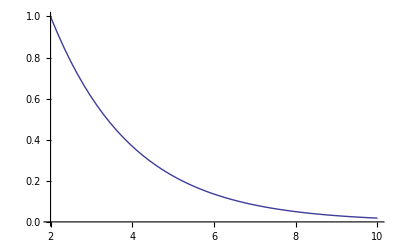

```mathematica
Plot[Exp[1/(1-(1/(1-2/r)))],{r,2,10}]
```

```mathematica
(* Then can do Trrnew = Trr*(1+x) + Ttt*x where x = Exp[1/(1-Gammatov)] where Gammatov=1/(1-2*M/r) *)
```

```mathematica
Solve[1/(1-2*M/r)==10.,r]
```

{{r→2.22222 M}}

```mathematica
causegamma=1/(1-2*M/r)//.{M->0.405*r}
(* Shapiro & Tuek equation 9.5.26 *)
causegamma=1/(1-2*M/r)//.{M->r*4.0/9.0}
```

5.26316

9.

```mathematica
4.0/9.0
```

0.444444

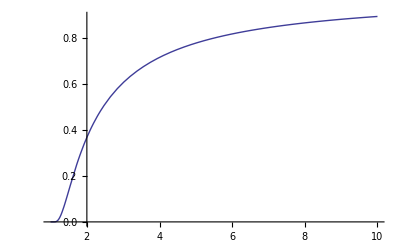

```mathematica
Plot[Exp[1/(1-ga)],{ga,1,10}]
```

```mathematica
(* So can set xtrue = MAX(0,x[gam],x[gam=gamcause] , where gamcause=gam[M/R=0.405] *)
```

```mathematica
FullSimplify[Exp[1/(1-g)]-Exp[1/(1-gl)]]
```

ⅇ^(1/(1-g))-ⅇ^(1/(1-gl))

```mathematica
FullSimplify[Exp[1/(1-g)]-Exp[-(1-g)]]
```

ⅇ^(1/(1-g))-ⅇ^(-1+g)

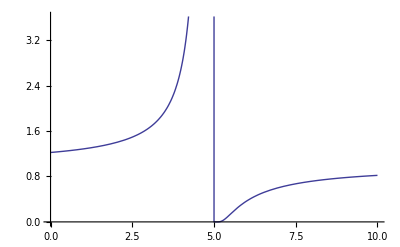

```mathematica
Plot[Exp[1/(1-(g-(5-1)))],{g,0,10}]
```

```mathematica
fun1=Exp[1/(5-g)]
fun2=If[g<5,0,fun1]
```

ⅇ^(1/(5-g))

If[g<5,0,fun1]

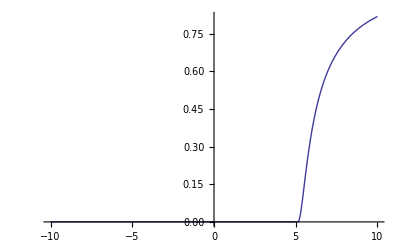

```mathematica
Plot[fun2,{g,-10,10}]
```

```mathematica
Plot[Exp[1/(5-g)],{g,0,10}]
```

-Graphics-

```mathematica
(* See how to convert TOV -> Kerr BH *)
```

```mathematica
solM=Solve[(2 M x)/(x^2+a^2 Cos[y]^2)==2*MBH/x,M]
sola=Solve[-(2 a MBH Sin[y]^2)/x==gtp,a]
fsnew=FullSimplify[gcovks//.solM[[1]]]//.sola[[1]]
(*fsnew=FullSimplify[gcovks//.solM[[1]]]*)
(*fsnew=FullSimplify[gcovks]*)
gcovksa0=FullSimplify[gcovks//.{a->0}]
MatrixForm[FullSimplify[fsnew-gcovksa0//.{M->MBH}]]
```

{{M→(MBH (x^2+a^2 Cos[y]^2))/x^2}}

{{a→-(gtp x Csc[y]^2)/(2 MBH)}}

{{-1+(2 MBH)/x,(2 MBH)/x,0,gtp},{(2 MBH)/x,1+(2 MBH)/x,0,(gtp (2 MBH+x))/(2 MBH)},{0,0,x^2+(gtp^2 x^2 Cot[y]^2 Csc[y]^2)/(4 MBH^2),0},{gtp,(gtp (2 MBH+x))/(2 MBH),0,((x^3+(gtp^2 x^2 (MBH+x) Csc[y]^4)/(4 MBH^2)-(gtp^2 x^2 Cos[2 y] Csc[y]^4)/(4 MBH)) Sin[y]^2)/x}}

{{-1+(2 M)/x,(2 M)/x,0,0},{(2 M)/x,1+(2 M)/x,0,0},{0,0,x^2,0},{0,0,0,x^2 Sin[y]^2}}

(0 | 0 | 0 | gtp
0 | 0 | 0 | gtp+(gtp x)/(2 MBH)
0 | 0 | (gtp^2 x^2 Cot[y]^2 Csc[y]^2)/(4 MBH^2) | 0
gtp | gtp+(gtp x)/(2 MBH) | 0 | (gtp^2 x (2 MBH+x Csc[y]^2))/(4 MBH^2))

```mathematica
MatrixForm[gcovks]
```

(-1+(2 M x)/(x^2+a^2 Cos[y]^2) | (2 M x)/(x^2+a^2 Cos[y]^2) | 0 | -(2 a M x Sin[y]^2)/(x^2+a^2 Cos[y]^2)
(2 M x)/(x^2+a^2 Cos[y]^2) | 1+(2 M x)/(x^2+a^2 Cos[y]^2) | 0 | -a (1+(2 M x)/(x^2+a^2 Cos[y]^2)) Sin[y]^2
0 | 0 | x^2+a^2 Cos[y]^2 | 0
-(2 a M x Sin[y]^2)/(x^2+a^2 Cos[y]^2) | -a (1+(2 M x)/(x^2+a^2 Cos[y]^2)) Sin[y]^2 | 0 | Sin[y]^2 (x^2+a^2 Cos[y]^2+a^2 (1+(2 M x)/(x^2+a^2 Cos[y]^2)) Sin[y]^2))

```mathematica
(gtp x)/(2 MBH)//.{gtp->-(2 a MBH Sin[y]^2)/x}
```

-a Sin[y]^2

```mathematica
(gtp^2 x (x Csc[y]^2))/(4 MBH^2)//.{gtp->-(2 a MBH Sin[y]^2)/x}
```

a^2 Sin[y]^2

```mathematica
FullSimplify[(gtp^2 x (2 MBH))/(4 MBH^2)]
```

(gtp^2 x)/(2 MBH)

```mathematica
test=FullSimplify[gcovks//.{y->Pi/2,a->J/M}]
MatrixForm[test]
```

{{-1+(2 M)/x,(2 M)/x,0,-(2 J)/x},{(2 M)/x,1+(2 M)/x,0,-(J (2 M+x))/(M x)},{0,0,x^2,0},{-(2 J)/x,-(J (2 M+x))/(M x),0,x^2+(J^2 (2 M+x))/(M^2 x)}}

(-1+(2 M)/x | (2 M)/x | 0 | -(2 J)/x
(2 M)/x | 1+(2 M)/x | 0 | -(J (2 M+x))/(M x)
0 | 0 | x^2 | 0
-(2 J)/x | -(J (2 M+x))/(M x) | 0 | x^2+(J^2 (2 M+x))/(M^2 x))